```mathematica
ω=1/GoldenRatio;
fib[i_]:=IntegerPart[(i+1)ω]-IntegerPart[i ω];
```

```mathematica
(* chain length *)
n=13;
L=Fibonacci[n];
(* stiffness couplings *)
delta=5.;
stiff[i_]:=(1+delta*fib[i-1]);
(* Ω matrix *)
subdiag=Table[{i,i+1}->-stiff[i],{i,1,L-1}];
diag=Table[{i,i}->stiff[i-1]+stiff[i],{i,2,L}];
PrependTo[diag,{1,1}->stiff[1]];
diagΩ2=Normal[SparseArray[diag,{L,L}]];
subdiagΩ2=Normal[SparseArray[subdiag,{L,L}]];
Ω2=subdiagΩ2+Transpose[subdiagΩ2]+diagΩ2;
```

```mathematica
eigmod=Sort[Sqrt[Eigenvalues[Ω2]]];
```

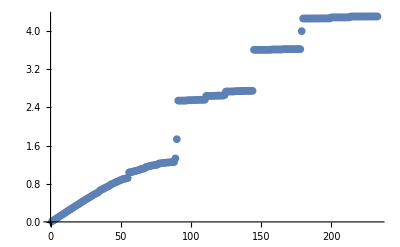

```mathematica
ListPlot[eigmod,Joined->False]
```